# Lab 3: Plotting --Carter Colton

```mathematica
Clear["`*" ]
```

## Assignment 1: Sin, Cos, Tan Graphs with Options

Make a plot of sinx, cosx, and tanx functions from -2π to 2π with a single Plot command. Make the three functions have different colors. Make one solid, one dashed, and one dotted. Use Exclusions→{-3Pi/2,-Pi/2,Pi/2,3Pi/2} as an option for the tangent function so that it doesn’t plot a line through the graph as tangent crosses over from +∞ to -∞. Give the plot a title, along with x- and y-axes labels. Pick an appropriate ImageSize and AspectRatio. Include GridLines if you feel like it.

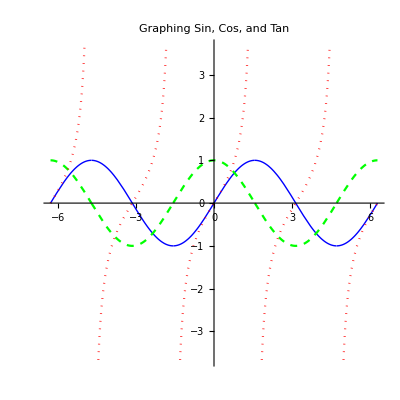

```mathematica
Plot[{Sin[x],Cos[x],Tan[x]}, {x,-2*Pi, 2*Pi}, PlotStyle->{{Blue, Thick},{Green,Dashed},{Red,Dotted}},Exclusions->{-3Pi/2,-Pi/2,Pi/2,3Pi/2},PlotLabel->"Graphing Sin, Cos, and Tan", FrameLabel->{Style["time (s)"],Style["Position (m)"]},ImageSize->400,AspectRatio->1]
```

## Assignment 2: Improve the Sin(1/x) Plot

Use PlotPoints and/or MaxRecursion to improve the LogLinearPlot of sin(1/x) from above, so that the oscillations near the origin clearly extend from -1 to 1.

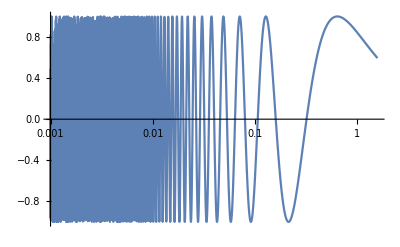

```mathematica
LogLinearPlot[Sin[1/x],{x,0.001,Pi/2},PlotRange->All]
```

```mathematica
f[x_]=Sin[1/x]
```

Sin[1/x]

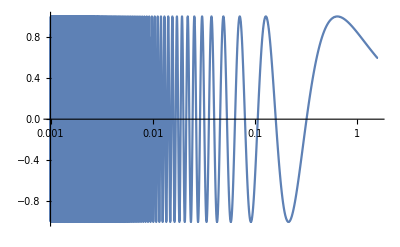

```mathematica
LogLinearPlot[f[x],{x,0.001,Pi/2},PlotRange->All,Mesh->All,PlotStyle->PointSize[0.001],PlotPoints->500,MaxRecursion->Automatic]
```

## Assignment 3: A Few Log Scale Plots

(a) Use LogPlot, LogLinearPlot and LogLogPlot to graph e^x over the range from x = 0.01 to 100.  Which log-scale scheme produced linear output and why? Be sure you can explain this.
(b) Repeat for ln(x). Hint: The natural log function in Mathematica is not called “Ln”.
(c) Repeat for x^3.

```mathematica
g[x_]=E^x
h[x_]=Log[x]
i[x_]=x^3
```

ⅇ^x

Log[x]

x^3

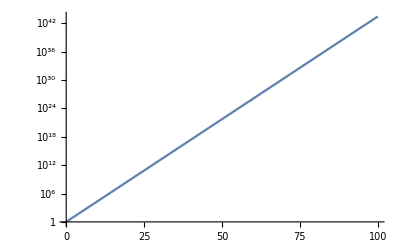

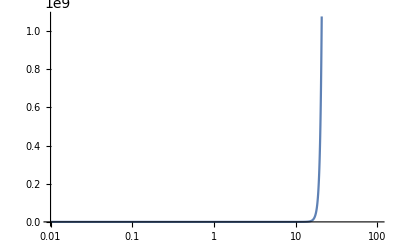

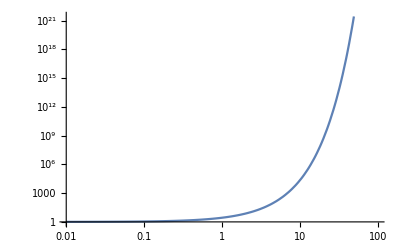

```mathematica
LogPlot[g[x],{x,.01,100}]
LogLinearPlot[g[x],{x,0.01,100}]
LogLogPlot[g[x],{x,0.01,100}]
```

LogPlot produced a linear output because LogPlot just takes the function to a single log. Since the function is e^x, the log and the e both cancel to leave us with only x. The other functions apply more functions than just one log to e, so they are not linear.

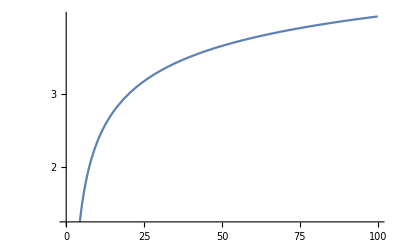

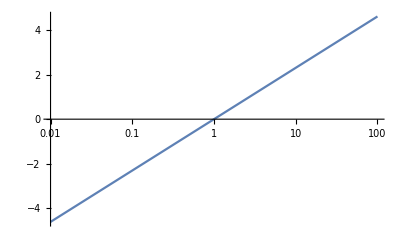

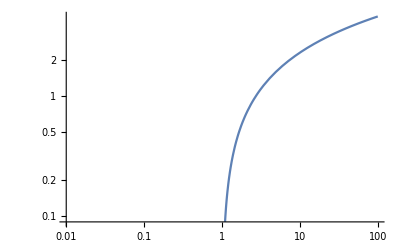

```mathematica
LogPlot[h[x],{x,0.01,100}]
LogLinearPlot[h[x],{x,0.01,100}]
LogLogPlot[h[x],{x,0.01,100}]
```

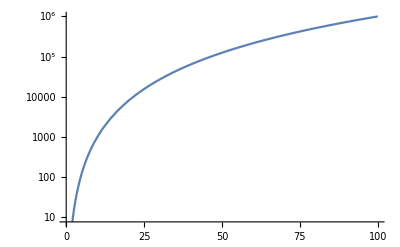

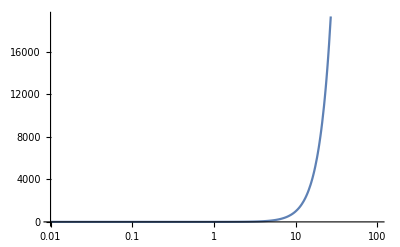

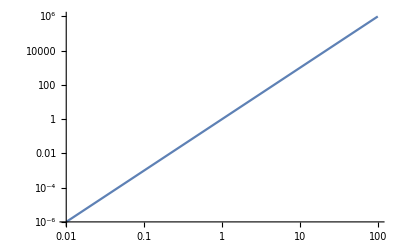

```mathematica
LogPlot[i[x],{x,0.01,100}]
LogLinearPlot[i[x],{x,0.01,100}]
LogLogPlot[i[x],{x,0.01,100}]
```

LogLinearPlot takes the Log of the y-axis and linearizes the x-axis. Doing this for a natural log function undoes what was done to the y-axis and makes the x-axis linear so that the overall function comes out as linear. LogLogPlot takes the Log twice, and since the function was x^3, that brings the function down 2 degrees, making it just x, so linear.

## Assignment 4: A Plot 3D Example

Use Plot3D to graph (x^2+y^2+0.1)^-1 over a sufficiently wide range of x and y to properly illustrate the central peak.  Apply PlotRange to prevent the top of the peak from getting clipped off.  Hide the Mesh and employ a ColorFunction to change the appearance with a different color gradient. (See the guide page on Color Schemes for a list of many of the built-in color gradients.) Use BoxRatios (analogous to AspectRatio in 2D graphics) to make the bounding box be cubic (i.e. BoxRatios → {1,1,1}).  Use Boxed (analogous to Frame in 2D graphics) to hide the bounding box, and also hide the Axes.  Apply FaceGrids → All to further customize the plot.

```mathematica
newfunction[x_]=(x^2+y^2+0.1)^-1
```

1/(0.1+x^2+y^2)

```mathematica
Plot3D[newfunction[x],{x,-3,3},{y,-3,3},PlotRange->All,ColorFunction->"BlueGreenYellow",BoxRatios->{1, 1, 1},Boxed->False,Axes->False,FaceGrids->All]
```

-Graphics3D-

## Assignment 5: Visualizing 3D Space as Contours

Use both ContourPlot and Plot3D to visualize the two-variable expression cos(π x) + cos(π y) over a range that extends from -2 to 2 along both axes.  Compare and contrast the two methods of plotting the function, and be able to explain to the TA how the one is a contour visualization of the other.

```mathematica
function[x_]=Cos[Pi*x]+Cos[Pi*y]
```

Cos[π x]+Cos[π y]

-Graphics3D-

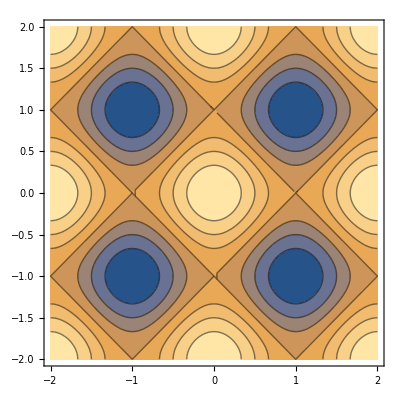

```mathematica
Plot3D[function[x],{x,-2,2},{y,-2,2},PlotRange->All]
ContourPlot[function[x],{x,-2,2},{y,-2,2}]
```

## Assignment 6: Solutions to Complicated Simultaneous Equations

Determine approximate (x,y) coordinates of the eight solutions to these two simultaneous equations:  cos(πx)+cos(πy)=0.5  and  x^2+y^2=2.  Do this graphically by sending a list of the two equations to ContourPlot (so the contours of both equations get plotted on the same graph); the intersection of the two sets of contours will reveal the points that are solutions to both. Use ContourStyle to make the two sets of contours appear with colors different than the default.

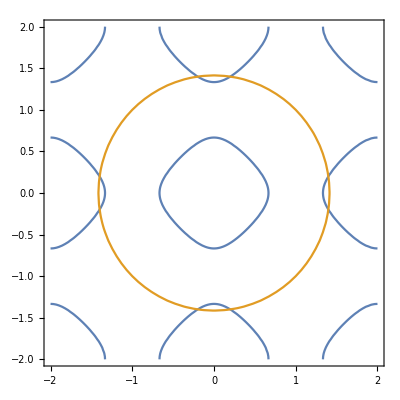

```mathematica
ContourPlot[{Cos[Pi*x]+Cos[Pi*y]==0.5,x^2+y^2==2},{x,-2,2},{y,-2,2}]
```

## Assignment 7: Electric Field From 2 Point Charges

A more interesting picture is the field from two point charges. To get a two-charge picture, there are two things you need to know in order to modify the equations appropriately. First, the charges will no longer be at the origin. Therefore, you need to know that the field at (x,y) from a charge located at the point (x0,y0) is just the same equation given above, but with x replaced by x-x0  and  y replaced by y-y0, everywhere in the equation. Second, the total field at (x,y) is the sum of the fields produced by each charge. With those in mind, do the following:

(a) Make a VectorPlot* and a StreamPlot** of the field from two like charges: one at x = 0.5 and one at x = -0.5. 
(b) Repeat, for two charges of opposite signs (a so-called "electric dipole"). To get the appropriate contribution from the negative charge, just use q = 1 in your starting equation.

* Hint: I found VectorPoints->10 to work well.
** Remember StreamPlot doesn’t use the VectorPoints option.

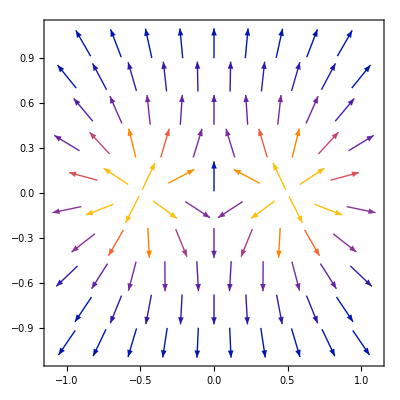

```mathematica
VectorPlot[{(x-.5)/((x-.5)^2+y^2)^1.5+(x+.5)/((x+.5)^2+y^2)^1.5,y/((x-.5)^2+y^2)^1.5+y/((x+.5)^2+y^2)^1.5},{x,-1,1},{y,-1,1}, VectorPoints->10]
```

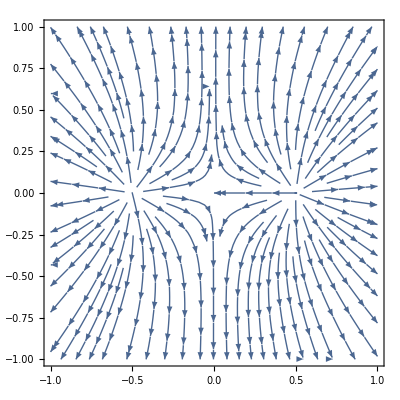

```mathematica
StreamPlot[{(x-.5)/((x-.5)^2+y^2)^1.5+(x+.5)/((x+.5)^2+y^2)^1.5,y/((x-.5)^2+y^2)^1.5+y/((x+.5)^2+y^2)^1.5},{x,-1,1},{y,-1,1}]
```

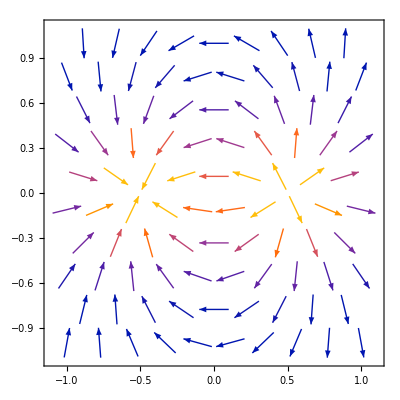

```mathematica
VectorPlot[{(x-.5)/((x-.5)^2+y^2)^1.5-(x+.5)/((x+.5)^2+y^2)^1.5,y/((x-.5)^2+y^2)^1.5-y/((x+.5)^2+y^2)^1.5},{x,-1,1},{y,-1,1}, VectorPoints->10]
```

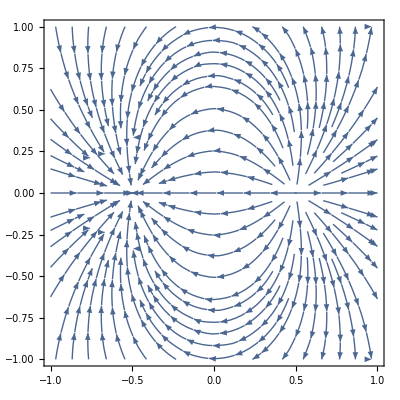

```mathematica
StreamPlot[{(x-.5)/((x-.5)^2+y^2)^1.5-(x+.5)/((x+.5)^2+y^2)^1.5,y/((x-.5)^2+y^2)^1.5-y/((x+.5)^2+y^2)^1.5},{x,-1,1},{y,-1,1}]
```

## Assignment 8: Plot of a Helix

A charged particle experiences a force from a magnetic field according to this equation:  F = qv×B, where q is the magnitude of the charge, v is the charge’s velocity, and B is the magnetic field at the location of the charge. This is sometimes called the Lorentz force. (We’ll assume for now that there is no electric field present.) Suppose the magnetic field is in the z-direction. If the particle is traveling in the z-direction, the cross product results in no force on the particle (because ẑ×ẑ=0). It is completely unaffected by the field. Conversely, if the particle is traveling only in the x-y plane, the cross product means that the force will always be perpendicular to the velocity. That causes circular motion, just like a ball on a string being spun in a circle where the tension force is always perpendicular to the velocity of the ball. If the particle has a combination of all three components, there will be circular motion in the x-y plane superimposed with a constant velocity in the z-direction. That produces a helix. 

Make a 3D parametric plot of such a helix. The x-coordinate should be proportional to cos(ωt), the y-coordinate proportional to sin(ωt), and the z-coordinate just proportional to  t  itself. Be able to explain those three choices. Pick a suitable choice of ω to get a good looking plot. Some trial and error might be in order.

```mathematica
ω=4;
x[t_] = Cos[ω*t];
y[t_] = Sin[ω*t];
z[t_]=t;
ParametricPlot3D[{x[t],y[t],z[t]},{t,0,10}]
```

-Graphics3D-

## Assignment 9: Using “show” With Different Types of Plots

(a) As mentioned in lab 1, Show can be used to merge two plots together. Use Show to combine a list plot of the following “listdata” with a regular Plot of the function y=x^2, with x going from 0 to 2. 
(b) Suppose plot1 is the plot of the data points and plot2 is the plot of the function. Figure out when there is a difference between Show[plot1,plot2] and Show[plot2,plot1]. Hint: try plotting y(x) with x going from 0 to 3.

```mathematica
listdata={{0., 0.}, {0.1, 0.1}, {0.2, 0.}, {0.3, 0.2}, {0.4, 0.2}, {0.5, 0.3}, {0.6, 0.4}, {0.7, 0.5},  {0.8, 0.7}, {0.9, 0.9}, {1., 1.}, {1.1, 1.3}, {1.2, 1.4}, {1.3, 1.7}, {1.4, 2.1}, {1.5, 2.3},  {1.6, 2.5}, {1.7, 2.9}, {1.8, 3.4}, {1.9, 3.7}, {2., 3.9}}
```

{{0.,0.},{0.1,0.1},{0.2,0.},{0.3,0.2},{0.4,0.2},{0.5,0.3},{0.6,0.4},{0.7,0.5},{0.8,0.7},{0.9,0.9},{1.,1.},{1.1,1.3},{1.2,1.4},{1.3,1.7},{1.4,2.1},{1.5,2.3},{1.6,2.5},{1.7,2.9},{1.8,3.4},{1.9,3.7},{2.,3.9}}

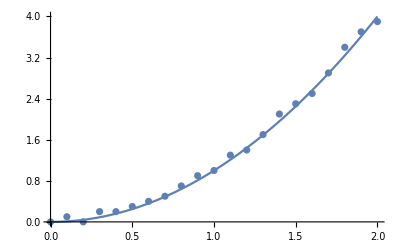

```mathematica
Show[Plot[x^2,{x,0,2}],ListPlot[listdata]]
```

The last and first examples are different from the rest.

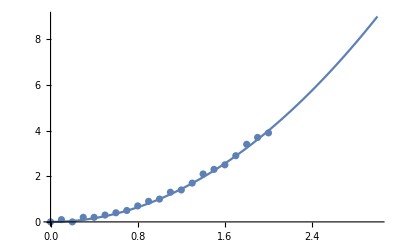

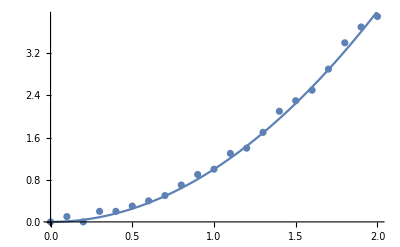

-Graphics-

-Graphics-

```mathematica
Show[Plot[x^2,{x,0,3}],ListPlot[listdata]]
Show[ListPlot[listdata],Plot[x^2,{x,0,3}]]
Show[ListPlot[listdata],Plot[x^2,{x,0,3}]]
Show[Plot[x^2,{x,0,3}],ListPlot[listdata]]
```

## Assignment 10: Combining Cosine Waves

When you add two sinusoidal waves together that have different amplitudes and phases but the same frequency, the result will always be a sinusoidal wave with the same frequency, but with yet another amplitude and phase. Those of you who took Phys 123 from me should even know how to calculate the amplitude and phase of the resulting function using complex numbers. For this assignment we'll determine the amplitude and phase of the sum through trial and error in a manipulatable graph.

(a) Define a function, y_1(t) = A_1 cos(5t + ϕ_1), where the amplitude A_1 and phase ϕ_1 are each given by  RandomReal[{0.1, 4}]  commands. Do the same for a second function, y_2. Plot them both together from 0 to 2π, and observe that their periods are each 2π/5. 

(b) Add the two functions together to obtain y_3(t):  y3[t_] = y1[t] + y2[t].  Plot it and notice that y_3(t)  also has a period of 2π/5. 

(c) Now, plot y3(t) on the same graph as a fourth function, Acos(5 t+ ϕ), where A and ϕ are parameters you can manipulate. Have A going from 0 to 8 and ϕ going from 0 to 2π. Plot y3 and this manipulatable function for times between 0 and 2π. Adjust your parameters manually until the two curves match up, and then read off the final values of the parameters by clicking on the + signs by the sliders.

```mathematica
y1[t_]=A1/.A1->RandomReal[{0.1,4}]*Cos[5*t+phi1/.phi1->RandomReal[{0.1,4}]]
```

0.672183 Cos[3.82617+5 t]

```mathematica
y2[t_]=A2/.A2->RandomReal[{0.1,4}]*Cos[5*t+phi2/.phi2->RandomReal[{0.1,4}]]
```

0.337331 Cos[0.228956+5 t]

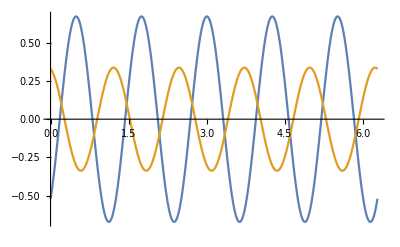

```mathematica
Plot[{y1[t],y2[t]},{t,0,2*Pi}]
```

```mathematica
y3[t_]=y1[t]+y2[t]
```

0.337331 Cos[0.228956+5 t]+0.672183 Cos[3.82617+5 t]

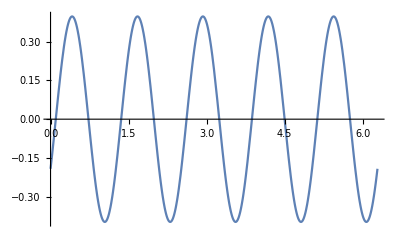

```mathematica
Plot[y3[t],{t,0,2*Pi}]
```

```mathematica
Manipulate[Plot[{y3[t],A4*Cos[5*t+phi4]},{t,0, 5}], {A4,0,8},{phi4,0,2*Pi}]
```

## Assignment 11: A Square Inscribed in a Circle

Use Graphics objects to inscribe a blue square inside a solid red disk.The disc should have radius 1 and be centered at the origin. Show the axes with an  Axes→True  option in your Graphics command. Hints: (1) The graphics objects you will need are called Rectangle and Disk. Create a few individual rectangles & disks to get a feel for those commands before trying to put them together. (2) The positions of the square’s corners will be related to the disk’s radius through the square root of 2:  the upper right corner = (cos45°, sin45°), for example.

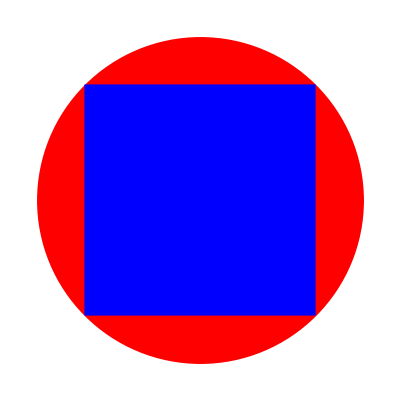

```mathematica
Graphics[{Red,Disk[],Blue,Rectangle[{-Sqrt[2]/2,-Sqrt[2]/2},{Sqrt[2]/2,Sqrt[2]/2}],Axes->True}]
```

## Assignment 12: Combining Traveling Waves

A traveling plane wave has the form ACos[kx - ωt], where A is the amplitude of the wave, k is the "wave number" = 2π/wavelength (how many radians of oscillation there are each meter for a frozen instant in time), and ω is the angular frequency = 2π/period (how many radians of oscillation there are each second at a fixed location in space). The speed of the wave  v = wavelength × frequency = (2π/k) × (ω/2π) = ω/k. 

Define a traveling wave function with A = 1 (in some units), k = 4 rad/m and ω = 2 rad/s. 
(a) Animate the plot in time (0 to 10 s) over the spatial region from 0 to 10 m. (Be sure to use the  Background→White  option for all your animations if you do your work in this notebook.) 
(b) Simultaneously animate a left moving wave, ACos[kx + ωt]. 
(c) Animate the sum of the two waves. Fix the y-axis scale using the PlotRange option so that it doesn’t continuously rescale on you. What is this? 
(d) Animate the sum of two right going waves, but change one to have k = 5 rad/m and ω = 2.5 rad/s  (note that ω/k, the wave's velocity, is the same for both). What is this?

```mathematica
travelingwave[x_,t_]=Cos[4*x-2*t]
```

Cos[2 t-4 x]

```mathematica
Animate[Plot[travelingwave[x,t],{x,0,10}],{t,0,10}]
```

```mathematica
travelingwaveleft[x_,t_]=Cos[4*x+2*t]
```

Cos[2 t+4 x]

```mathematica
Animate[Plot[{travelingwave[x,t],travelingwaveleft[x,t]},{x,0,10}],{t,0,10}]
```

```mathematica
Animate[Plot[travelingwave[x,t]+travelingwaveleft[x,t],{x,0,10},PlotRange->{{0,10},{-3,3}}],{t,0,10}]
```

```mathematica
travelingwaveright[x_,t_]=Cos[5*x-2.5*t]
```

Cos[2.5 t-5 x]

```mathematica
Animate[Plot[travelingwave[x,t]+travelingwaveright[x,t],{x,0,10}],{t,0,10}]
```

## Assignment 13: Magnetic Field From a Wire

Magnetic fields are produced by currents of charges. The magnetic field produced at position (x,y) by a current flowing in a very long, straight wire on the z-axis is given by this equation: B=((μ_0 I)/(2π))(-y x̂  +  x ŷ)/(x^2+y^2). Here I is the current (in amps) and μ_0 is a fundamental constant... but for our purposes you can set the stuff inside the parentheses equal to 1. Use VectorPlot3D to visualize this field over the range from -1 to +1 in all three directions. Hint: use the unit vectors in the equation to break B into B_x, B_y, and B_z components (B_z=0).

```mathematica
magneticfunction[x_,y_]=(-y x̂  +  x ŷ)/(x^2+y^2)
```

(-y x̂+x ŷ)/(x^2+y^2)

```mathematica
VectorPlot3D[magneticfunction[x,y],{x,-1,1},{y,-1,1},VectorPoints->10]
```

VectorPlot3D::argrx: VectorPlot3D called with 3 arguments; 4 arguments are expected.

VectorPlot3D[magneticfunction[x,y],{x,-1,1},{y,-1,1},VectorPoints→10]